```mathematica
(*This will do the heat equation in 1D*)
alpha = 0.01;
sol = NDSolve[{{D[u1[x,t],t]==alpha*D[u1[x,t],{x,2}]},{u1[x,0]==-5*x*(x-1)},{u1[0,t]==0},{u1[1,t]==0}},u1,{x,0,1},{t,0,10}]
```

{{u1→InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]}}

```mathematica
Manipulate[Plot[{k*x(x-1),0*x+10},{x,0,1}],{k,-20,5}]
```

```mathematica
Manipulate[Plot[{Evaluate[u1[x,t]/.sol],0*x+1.3},{x,0,1}],{t,0,10}]
```

```mathematica
(*This will do the heat equation in 2D*)
```

```mathematica
alpha2 = 0.003;
sol2 = NDSolve[{{D[u2[x,y,t],t]==alpha2*(D[u2[x,y,t],{x,2}]+D[u2[x,y,t],{y,2}])},{u2[x,y,0]==10*x*(x-1)*y*(y-1)},{u2[0,y,t]==0},{u2[1,y,t]==0},{u2[x,0,t]==0},{u2[x,1,t]==0}},u2,{x,0,1},{y,0,1},{t,0,20}]
```

{{u2→InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 20.}}, <>]}}

```mathematica
Plot3D[{10*x*(x-1)*y*(y-1),0*x*y},{x,-1,2},{y,-1,2}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[{Evaluate[u2[x,y,t]/.sol2],{0*x*y+0.7}},{x,0,1},{y,0,1}],{t,0,20}]
```

```mathematica
(*Goal is to make PDE over the following mesh*)
```

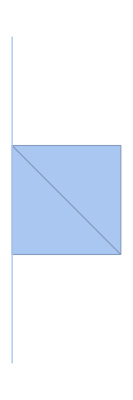

```mathematica
meshMixed = MeshRegion[ {{0,0},{0,1},{0,2},{0,3},{1,1},{1,2}}, {Line[{1,4}],Simplex[{2,3,5}],Simplex[{3,5,6}]}]
```